# Support Vector Machines

In this notebook we will develop support vector machine models for several datasets by using them to formulate a constrained optimisation problem. First, we review how constrained optimisation is done in Mathematica.

## Constrained Optimisation

Consider the problem of minimising x^2+y^2 subject to the constraints 3x+2y≥7 and x+2y≥6. We can solve this using NMinimize:

```mathematica
NMinimize[{x^2+y^2,3 x+2 y≥7&&x+2 y≥6},{x,y}]
```

{7.2,{x→1.2,y→2.4}}

```mathematica
NMinimize[{x^2+y^2,And[3 x+2 y≥7,x+2 y≥6]},{x,y}]
```

{7.2,{x→1.2,y→2.4}}

Let’s visualise the solution along with the constraints and the function we are trying to minimise.

```mathematica
Show[Plot3D[x^2+y^2,{x,0,5},{y,0,5},RegionFunction->Function[{x,y},3 x+2 y≥7&&x+2 y≥6]],Graphics3D[{Opacity[0.5],Gray,InfinitePlane[Table[{x,0.5 (7-3 x),RandomReal[]},{x,3}]]}],Graphics3D[{Opacity[0.5],Gray,InfinitePlane[Table[{x,0.5 (6-x),RandomReal[]},{x,3}]]}]]
```

-Graphics3D-

## Linear Support Vector Machine

Let’s now produce a support vector machine for the example from the video lectures. First, we need to define the samples, x_i. These are points in a 2D vector space which are labelled as either “Plus” or “Minus”.

```mathematica
data=<|"Plus"->{{1.284422952732416,2.481901856407326},{1.4879960382523703,2.402086883623099},{4.193340935618989,2.0674820899685353},{1.07511361074236,2.8655605261563037},{4.5621522276001985,2.3036590135818598},{0.0734941576442104,2.7567100412409644},{2.0267587486366514,1.8146817202743937},{1.7160467347301873,2.2314527869285374}},"Minus"->{{0.3650725217541822,1.4540111456859945},{1.8799169703454597,1.3235540770631689},{0.2775167301897557,0.026781782266628973},{1.7185797382262036,0.8439744313421516},{1.0440125841941863,0.8714161830961258},{4.009012707820185,0.4883132746354524},{0.0444111436444237,1.0249991478151106},{1.4175016236764821,0.3949618274790252},{0.40287782851680287,0.35796696425588426},{1.3129335119181957,0.193320544474747},{1.6678854129083547,0.5245058562945744},{3.62477502445507,0.2321920742831569}}|>;
```

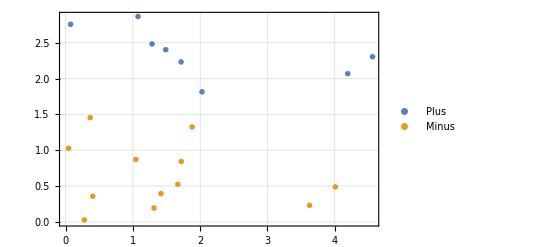

```mathematica
ListPlot[data,PlotMarkers->"OpenMarkers",PlotTheme->"Detailed"]
```

### Solving the primal problem

We can directly solve the primal problem. To do so we need to set up the constraints imposed by the samples.

```mathematica
plusConstraints=Apply[And,Table[{w1,w2}.x+b≥1,{x,data["Plus"]}]]
```

b+1.28442 w1+2.4819 w2≥1&&b+1.488 w1+2.40209 w2≥1&&b+4.19334 w1+2.06748 w2≥1&&b+1.07511 w1+2.86556 w2≥1&&b+4.56215 w1+2.30366 w2≥1&&b+0.0734942 w1+2.75671 w2≥1&&b+2.02676 w1+1.81468 w2≥1&&b+1.71605 w1+2.23145 w2≥1

```mathematica
minusConstraints=Apply[And,Table[{w1,w2}.x+b≤-1,{x,data["Minus"]}]]
```

b+0.365073 w1+1.45401 w2≤-1&&b+1.87992 w1+1.32355 w2≤-1&&b+0.277517 w1+0.0267818 w2≤-1&&b+1.71858 w1+0.843974 w2≤-1&&b+1.04401 w1+0.871416 w2≤-1&&b+4.00901 w1+0.488313 w2≤-1&&b+0.0444111 w1+1.025 w2≤-1&&b+1.4175 w1+0.394962 w2≤-1&&b+0.402878 w1+0.357967 w2≤-1&&b+1.31293 w1+0.193321 w2≤-1&&b+1.66789 w1+0.524506 w2≤-1&&b+3.62478 w1+0.232192 w2≤-1

```mathematica
allConstraints=Join[plusConstraints,minusConstraints]
```

b+1.28442 w1+2.4819 w2≥1&&b+1.488 w1+2.40209 w2≥1&&b+4.19334 w1+2.06748 w2≥1&&b+1.07511 w1+2.86556 w2≥1&&b+4.56215 w1+2.30366 w2≥1&&b+0.0734942 w1+2.75671 w2≥1&&b+2.02676 w1+1.81468 w2≥1&&b+1.71605 w1+2.23145 w2≥1&&b+0.365073 w1+1.45401 w2≤-1&&b+1.87992 w1+1.32355 w2≤-1&&b+0.277517 w1+0.0267818 w2≤-1&&b+1.71858 w1+0.843974 w2≤-1&&b+1.04401 w1+0.871416 w2≤-1&&b+4.00901 w1+0.488313 w2≤-1&&b+0.0444111 w1+1.025 w2≤-1&&b+1.4175 w1+0.394962 w2≤-1&&b+0.402878 w1+0.357967 w2≤-1&&b+1.31293 w1+0.193321 w2≤-1&&b+1.66789 w1+0.524506 w2≤-1&&b+3.62478 w1+0.232192 w2≤-1

Now we can use NMinimise to find the  solution to the constrained optimisation problem.

```mathematica
{norm2,sol}=NMinimize[{0.5 (w1^2+w2^2),allConstraints},{w1,w2,b}]
```

{7.61125,{w1→1.11765,w2→3.7381,b→-8.04866}}

This means that our decision function is

```mathematica
decision[x_]:={1.1176497303899737,3.738096096794236}.x+(-8.048661024444451)
```

```mathematica
decision[{1.2,1.3}]
```

-1.84796

Then, our decision line is

```mathematica
Solve[decision[{x,y}]==0,y]
```

{{y→0.267516 (8.04866-1.11765 x)}}

and our margins are

```mathematica
Solve[decision[{x,y}]==1,y]
```

{{y→0.267516 (9.04866-1.11765 x)}}

```mathematica
Solve[decision[{x,y}]==-1,y]
```

{{y→0.267516 (7.04866-1.11765 x)}}

Let’s now plot our decision line, margins and data points

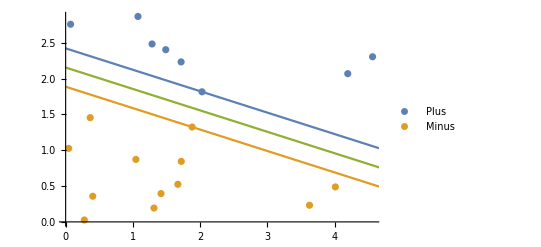

```mathematica
Show[ListPlot[data],Plot[{0.2675158621142974 (9.048661024444451-1.1176497303899737 x),0.2675158621142974 (7.048661024444451-1.1176497303899737 x),0.2675158621142974 (8.048661024444451-1.1176497303899737 x)},{x,0,5}]]
```

### Solving the dual problem

We could also solve the dual problem. First, we build up the matrix X and vectors y, λ and e.

```mathematica
X=Join[data["Plus"],-data["Minus"]]
```

{{1.28442,2.4819},{1.488,2.40209},{4.19334,2.06748},{1.07511,2.86556},{4.56215,2.30366},{0.0734942,2.75671},{2.02676,1.81468},{1.71605,2.23145},{-0.365073,-1.45401},{-1.87992,-1.32355},{-0.277517,-0.0267818},{-1.71858,-0.843974},{-1.04401,-0.871416},{-4.00901,-0.488313},{-0.0444111,-1.025},{-1.4175,-0.394962},{-0.402878,-0.357967},{-1.31293,-0.193321},{-1.66789,-0.524506},{-3.62478,-0.232192}}

```mathematica
Y=Join[ConstantArray[1,Length[data["Plus"]]],ConstantArray[-1,Length[data["Minus"]]]]
```

{1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
e=ConstantArray[1,Length[X]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
λ=Table[λi[i],{i,Length[X]}]
```

{λi[1],λi[2],λi[3],λi[4],λi[5],λi[6],λi[7],λi[8],λi[9],λi[10],λi[11],λi[12],λi[13],λi[14],λi[15],λi[16],λi[17],λi[18],λi[19],λi[20]}

Now we can solve the dual optimisation problem

```mathematica
{max,solλ}=NMaximize[{-0.5 λ.X.Transpose[X].λ+λ.e,λ≥0,λ.Y==0},λ]
```

{7.61125,{λi[1]→5.14165×10^-7,λi[2]→4.72833×10^-10,λi[3]→0.,λi[4]→0.,λi[5]→0.,λi[6]→2.81689×10^-8,λi[7]→7.61184,λi[8]→5.40358×10^-8,λi[9]→0.,λi[10]→7.61185,λi[11]→0.,λi[12]→0.,λi[13]→0.,λi[14]→0.,λi[15]→0.,λi[16]→0.,λi[17]→0.,λi[18]→0.,λi[19]→0.,λi[20]→0.}}

Notice that only a small number of the λ_i’s are non-zero; these are the ones corresponding to the support vectors.

We can next compute the value for w=X^T λ and find b from one of the constraints with a non-zero λ_i actually being an equality (rather than an inequality).

```mathematica
wsolλ=Thread[{w1,w2}->Transpose[X].λ/.solλ]
```

{w1→1.11774,w2→3.73839}

```mathematica
bsolλ=Solve[plusConstraints⟦7⟧/.wsolλ/.GreaterEqual->Equal,b][[1]]
```

{b→-8.04937}

Check this agrees with what we found when solving the primal version

```mathematica
sol
```

{w1→1.11765,w2→3.7381,b→-8.04866}

Knowing the support vectors, we could also go the other way and obtain the λ’s from the w and b found by solving the primal problem

```mathematica
Inverse[Transpose[X⟦{7,10}⟧.{w1,w2}]==
```

Again, this is consistent with solving the dual problem.

## Kernel Trick

We next look at an example where the data is not linearly separable and we will have to apply the kernel trick. First we generate two datasets, one surrounding another. We do this by defining the data in polar coordinates:

And then transforming to Cartesian coordinates:

We now have a non-linearly separable dataset:

### Explicit polar coordinate map

We first look at the case where we have a good idea for an explicit map ϕ(x,y)=(r,θ) that will transform the data into a nice form. Define the map and apply it to our data:

Now we build up our X matrix with the transformed samples

Now we can solve the dual optimisation problem

We can then compute the values for w=X^T λ, and find b from one of the constraints with a non-zero λ_i actually being an equality (rather than inequality).

Now we draw our decision line and margins on the r-θ plot

We can also draw them on the original plot

### Explicit higher map to higher dimensions

There is another way we could get support vector machines to work with this dataset: by projecting onto a higher dimension. We now try the map ϕ(x,y)=(x,y,x^2+y^2)

We go through the same process as before to set up the dual optimisation problem:

We now compute the values for w=X^T λ and find b from one of the constraints with a non-zero λ_i actually being an equality (rather than inequality).

Now we draw our decision line and margins on the r-θ plot

We can also draw them on the original plot

### Implicit map using the Kernel trick

Instead of defining the map explicitly, the fact that our optimisation only depends on the inner product of samples means we can use the kernel trick. Let’s define a kernel k((x_i,y_i),(x_j,y_j))=x_i x_j+y_i y_j+(x_i^2+y_i^2)(x_j^2+y_j^2)

We now set up the dual optimisation problem by computing X X^T directly using the kernel:

We have now found the solution. In fact, it’s the exact same solution as we found with the 3D map because this kernel is exactly the one you get from that map.

### Generic Kernels

In the example so far we had a good idea for which kernel to use a priori. That is not usually the case so let’s now look at using some generic kernels. We will apply it to the following dataset:

We could implement the kernels ourselves, take care of projecting back to the original space, etc., but let’s now just use the high-level Classify function to take care of all of those details for us. We will specify the “SupportVectorMachine” method with three different choices of kernel. Note that this generates a function that can return a probability that the input is of a given class.

First, with a linear kernel it fails totally

Next, the polynomial kernel does quite a good job in this case

The Gaussian/radial basis function kernel does a good job

## Handwriting recognition: Support Vector Machine with MNIST Digits dataset

We now return to the example of handwriting recognition to see how well support vector machines perform with categorising the MNIST Digits dataset

We will train our support vector machine with a random sample of 100 digits.

Let’s see how well it performs by testing it on a random sample of the test data

It’s right about 15% of the time - only slightly better than random luck. We could improve this by going back to the training step and using more training samples:

Let’s see how well it performs by testing it on a random sample of the test data

Now this is close to 90% accurate